```mathematica
Tcn={0,0.015197864,0.017863372,0.023256351,0.024702381,0,0,0.027519927,0.028030979,0.02496124,0.018514313,0};
ntot={0.75,0.8,0.85,0.9,0.95,1.0,1.05,1.1,1.15,1.2};
```

```mathematica
ntot2={0.75,0.8,0.85,0.9,0.95,0.975,1.0,1.025,1.05,1.1,1.15,1.2};
```

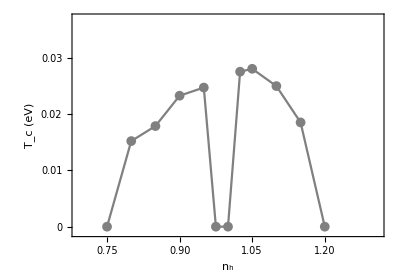

```mathematica
dcaTcvsn2by2Upp0=ListPlot[Table[{ntot2[[i]],Tcn[[i]]},{i,1,Length[ntot2]}],PlotMarkers->{Automatic,10},Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->17.5,FontFamily->"times New Roman"},FrameLabel->{{"T_c (eV)",None},{"n_h",None}},Joined->True,PlotRange->{{0.69,1.31},{-0.001,0.037}},FrameTicks->{{{0,0.01,0.02,0.03},Automatic},{Automatic,None}},PlotStyle->Gray]
```

```mathematica
dca2by2Upp0n105lambdavsT={{1/16,0.7675},{1/18,0.8069825725888563},{1/21,0.8603012618373805},{1/25,0.9152909310903398},{1/32,0.9767},{1/34,0.988572275},{1/35,0.99607882},{1/36,1.00183708}};
```

```mathematica
dca2by2Upp0n095lambdavsT={{1/16,0.7276},{1/18,0.7694118019642189},{1/21,0.8243017415671803},{1/25,0.8805431349948786},{1/32,0.9627},{1/34,0.969359715},{1/35,0.979998795},{1/36,0.98119138},{1/40,0.9995}};
```

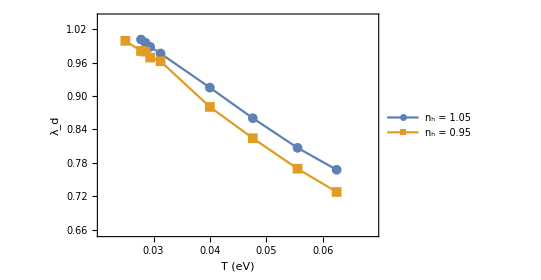

```mathematica
lambdad0two=ListPlot[{dca2by2Upp0n105lambdavsT,dca2by2Upp0n095lambdavsT},Frame->True,AspectRatio->0.7,BaseStyle->{FontSize->18,FontFamily->"times New Roman"},PlotLegends->Placed[LineLegend[{"n_h = 1.05","n_h = 0.95"},LabelStyle->{14},LegendLayout->{"Row",1}],{0.5,0.07}],FrameLabel->{"T (eV)","λ_d"},PlotRange->{{0.021,0.069},{0.655,1.04}},PlotMarkers->{Automatic,10},Joined->True]
```

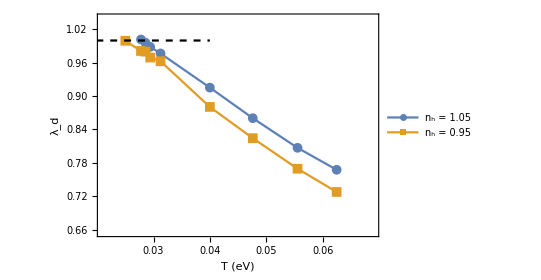

```mathematica
lambdadtwo=Show[lambdad0two(*,figlambdadn105,figlambdadn110,figlambdadn115*),line(*,Epilog->Inset[pdinvdiffc,{0.0263,0.6},Automatic,0.019]*)]
```